```mathematica
<<Units`
```

Convert::shdw: Symbol Convert appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

SolarMass::shdw: Symbol SolarMass appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
```

#### Trigger size as function of density (see Woosley, check with SR).

```mathematica
trigger[ρ_]:=Piecewise[{{10^-5*(ρ/(5*10^9))^(-1/2),ρ>10^8},{1/(10000 √2)*(ρ/10^8)^-2,ρ<=10^8}}]
```

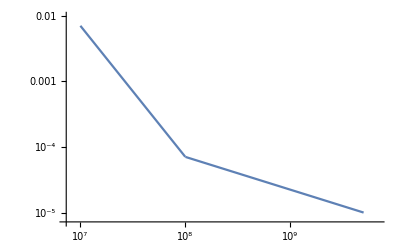

```mathematica
LogLogPlot[{trigger[ρ],δ[ρ]},{ρ,5*10^9,10^7}]
```

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
```

```mathematica
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
```

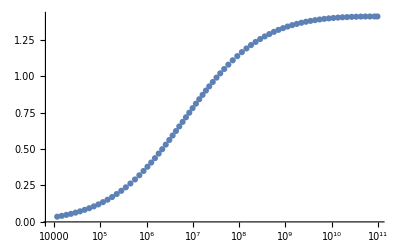

```mathematica
ListLogLinearPlot[WD]
```

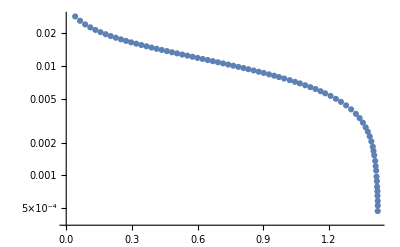

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Massreverse=Interpolation[Reverse/@WD];
```

```mathematica
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### λ_T as function of mass

```mathematica
triggermass=Interpolation[Table[{WDplot[ρ],trigger[ρ]},{ρ,fSpace[10^6,5*10^9,1000]}]];
```

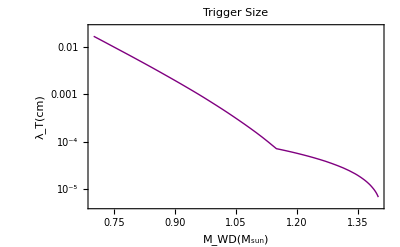

```mathematica
LogPlot[triggermass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### V_esc

```mathematica
Clear[vesc]
```

```mathematica
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

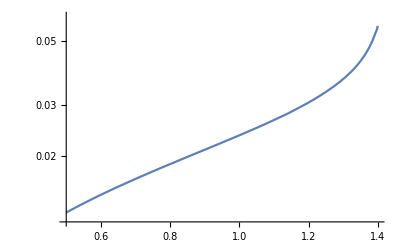

```mathematica
LogPlot[vesc[M],{M,0.5,1.4}]
```

#### τ_d (for trigger size) scales as 1/ρ by definition. Diffusion time vs. transit time comparision - need to check τ_d!

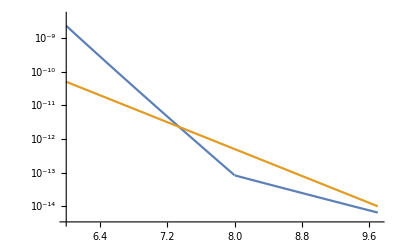

```mathematica
LogPlot[{Convert[(trigger[10^ρ]Centimeter)/(vesc[WDplot[10^ρ]]SpeedOfLight),Second] 1/Second,10^-14((5*10^9)/10^ρ)},{ρ,Log10[10^6],Log10[5*10^9]}]
```

#### Transit upper bound - flux is too low - for a single WD

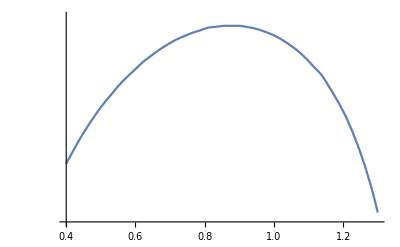

```mathematica
LogPlot[Convert[Subscript[ρ, DM] (Giga*ElectronVolt)/Centimeter^3*Giga Year*Pi*(Radplot[M]SolarRadius)^2*(vesc[M])^2/(10^-3)1/SpeedOfLight*SpeedOfLight^2,Giga ElectronVolt] 1/(Giga ElectronVolt)/.{Subscript[ρ, DM]->10^3},{M,0.4,1.3}]
```

#### Minimum E_boom for different densities

```mathematica
eboom[M_]:=Convert[(Massreverse[M]*Gram/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*4 Pi/3(triggermass[M]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d]
```

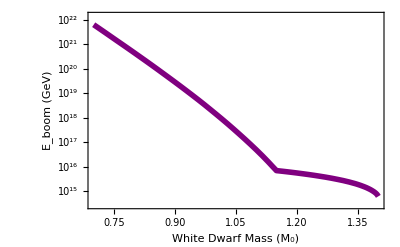

```mathematica
LogPlot[eboom[M],{M,0.7,1.4},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},Frame->True,FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### Crust stopping calculation (R_c~ km, ρ_c~ ρ_interior)

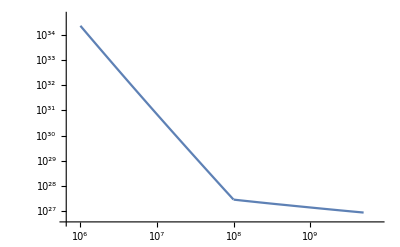

```mathematica
LogLogPlot[Convert[((Mega ElectronVolt)/vesc[WDplot[ρ]]^2(trigger[ρ]*Centimeter)^2*ρ Gram/Centimeter^3*1/(12 Giga ElectronVolt)*SpeedOfLight^2(1Kilo Meter))1/(Giga ElectronVolt),d],{ρ,10^6,5*10^9}]
```

#### Transit Constraint Plots - General

```mathematica
crustcondition=Log10[Convert[vesc[1.25]^2/(10^32 Centimeter^-3*1 Kilo Meter)10^mdm/ϵ,Centimeter^2] 1/Centimeter^2];
```

```mathematica
boomcondition=Log10[10^-3/ϵ*triggermass[1.25]^2];
```

```mathematica
boomcondition2=Log10[10^-3/ϵ*(0.00005856190096092564)^2];
```

```mathematica
crustplot=Plot[crustcondition/.ϵ->10^3,{mdm,25,50}];
```

```mathematica
photonboom=Plot[boomcondition/.ϵ->10^3,{mdm,25,50}];
```

```mathematica
electronboom=Plot[boomcondition2/.ϵ->10^3,{mdm,25,50}];
```

```mathematica
fluxlimit=Plot[( 100 Sign[x-48]),{x,24,50},ExclusionsStyle->Red,PlotRange->{-30,10}];
```

```mathematica
canvasconstraint=Plot[-100,{x,25,50},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(photon, TeV) (cm^2)"},PlotRange->{-30,10},Axes->None];
```

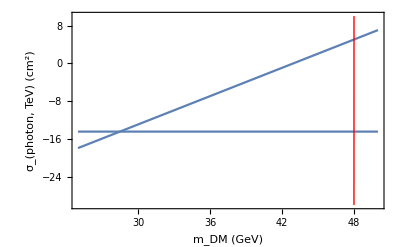

```mathematica
Show[canvasconstraint,crustplot,electronboom,fluxlimit]
```

#### Collision and Decay constraint

#### Observation:

```mathematica
eboom[1.25]
```

4.23537×10^15

```mathematica
Solve[(ρ/m)^2*σ*10^3*v*4 Pi/3 R^3==Γ,σ]
```

{{σ→(3 m^2 Γ)/(4000 π R^3 v ρ^2)}}

```mathematica
σobs=Convert[(3 m^2 Γ)/(4000 π R^3 v ρ^2)/.{Γ->1/(Giga Year),R->3000 Kilo Meter,m->m Giga ElectronVolt,v->10^-3 SpeedOfLight,ρ->0.4Giga ElectronVolt/Centimeter^3},Barn];
```

```mathematica
σobs
```

5.84521×10^-29 Barn m^2

```mathematica
σobs/.m->eboom[1.25]
```

1048.54 Barn

```mathematica
Solve[ρ/m*10*1/t*4 Pi/3 R^3==Γ,t]
```

{{t→(40 π R^3 ρ)/(3 m Γ)}}

```mathematica
decayobs=Convert[(40 π R^3 ρ)/(3 m Γ)/.{Γ->1/(Giga Year),R->3000 Kilo Meter,m->m Giga ElectronVolt,v->10^-3 SpeedOfLight,ρ->0.4Giga ElectronVolt/Centimeter^3},Giga Year];
```

```mathematica
decayobs
```

(4.52389×10^26 Giga Year)/m

#### SN Rate

```mathematica
eboom[0.85]
```

1.14774×10^20

```mathematica
snrate=0.3/Century;
```

```mathematica
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
Qfunction = (FullSimplify[Re[Integrate[whitedwarfdistribution[m], {m,x, ∞}]]]);
```

```mathematica
collSN=(0.4(Giga ElectronVolt)/Centimeter^3 1/(m Giga ElectronVolt))^2*σ*10^3*10^-3 SpeedOfLight*4 Pi/3*(3000 Kilo Meter)^3*10^10 Qfunction/.x->0.85;
```

```mathematica
Solve[collSN==snrate,σ]
```

{{σ→(8.27761×10^-29 Centimeter^6 m^2 Second)/(Century Kilo^3 Meter^4)}}

```mathematica
Convert[(8.277609171812806*^-29 Centimeter^6 m^2 Second)/(Century Kilo^3 Meter^4),Barn]/.m->eboom[0.85]
```

3.45767×10^9 Barn

```mathematica
decaySN=(0.4(Giga ElectronVolt)/Centimeter^3 1/(m Giga ElectronVolt))*10 4 Pi/3*(3000 Kilo Meter)^3*10^10 Qfunction/.x->1.2;
```

```mathematica
Convert[0.3/Century*1/(1/(Giga Year)),d]
```

3.×10^6

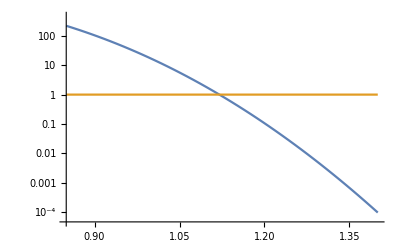

```mathematica
LogPlot[{10^10 Qfunction/(3 10^6),1},{x,0.85,1.4}]
```

```mathematica
Solve[decaySN*1/t==snrate,t]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→(4.77591×10^17 Century Kilo^3 Meter^3)/(Centimeter^3 m)}}

```mathematica
Convert[(4.7759107526302464*^17 Century Kilo^3 Meter^3)/(Centimeter^3 m),Giga Year]
```

(4.77591×10^25 Giga Year)/m

#### Q-ball boom

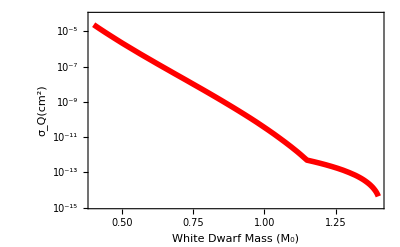

```mathematica
LogPlot[1/10^4*(triggermass[M])^2,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```